```mathematica
add=NotebookDirectory[];
data=Import[add<>"cl_planck_lensed","Table"];
kmin=Min[data[[Range[1,Length[data]],1]]];
kmax=Max[data[[Range[1,Length[data]],1]]];
p=Interpolation[data,Method->"Hermite",InterpolationOrder->3];
```

```mathematica
Sum[data[[i,2]],{i,1,4095}]
```

3393.10749656555506

```mathematica
180/7.2
```

25.

```mathematica
√(1.24 10^-8)
```

0.000111355

```mathematica
θ =180/l
```

```mathematica
data[[8,2]]
```

57.803908562650598

```mathematica
data[[4096,1]]
```

4097.

```mathematica
10^-6 √Sum[(2l+1)/(4π)p[l],{l,25,kmax}]
```

0.00010014948757475339

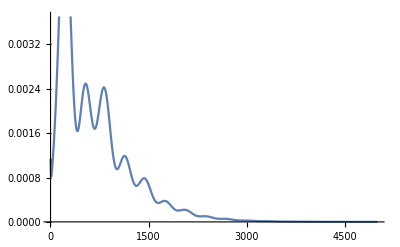

```mathematica
Plot[10^-6(l(l+1))/(2π)p[l],{l,2,5000}]
```

```mathematica
200(200+1)/(2π)p[200]
```

5449.10000000000002

```mathematica
data[[All,2]]
```